```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
(*accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/EVBK/gdc_VER_EVBK_points.txt"];*)
accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/POINTS/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"];
confDec100=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_INC/CONF_DECREASING_1.00.txt"];
confDec099=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_INC/CONF_DECREASING_0.99.txt"];
confDec095=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_INC/CONF_DECREASING_0.95.txt"];
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]];
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
spezAdd="CONF_INC/RAT_0_99/";
plotType="DEC";
revType="ALL";
(* col1=Map[ColorData["BlueGreenYellow"][#]&,Range[Length[timesteps]]/Length[timesteps]]
col3=Map[Hue[#]&,Range[Length[timesteps]]/Length[timesteps]]
col4=Map[Hue[1,#]&,Range[Length[timesteps]]/Length[timesteps]]
col5=Map[ColorData["TemperatureMap"][#]&,Range[Length[timesteps]]/Length[timesteps]]*)
```

{DLB,MUR,LYE,PHI,SED,AUS}

```mathematica
(* Dec>0.01 *)
dataDOJ=sumUpFunc[accEVBK, accCH,confDec099,"DOJ",names,revType];
dataZ=sumUpFunc[accEVBK, accCH,confDec099,"Z",names,revType];
dataF=sumUpFunc[accEVBK, accCH,confDec099,"F",names,revType];
```

```mathematica
(*shrinkFac1=0.005;
shrinkFac2=0.0;*)
shrinkFac1=0.02;
shrinkFac2=0.02;
plotsDOJ=Map[singlePlot[#, dataDOJ,col2,shrinkFac1,shrinkFac2,plotType]&,names];
gridDOJ=Grid[{plotsDOJ[[1;;2]],plotsDOJ[[3;;4]],plotsDOJ[[5;;6]]}];
plotsZ=Map[singlePlot[#, dataZ,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridZ=Grid[{plotsZ[[1;;2]],plotsZ[[3;;4]],plotsZ[[5;;6]]}];
plotsF=Map[singlePlot[#, dataF,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridF=Grid[{plotsF[[1;;2]],plotsF[[3;;4]],plotsF[[5;;6]]}];
```

size {0.112074,0.0751028,0.0379543,0.085349,0.105259}

size {0.0897583,0.102796,0.102526,0.096079}

size {0.0931154,0.102141}

size {0.0883423,0.0482322,0.0937776}

size {0.0787329,0.086197}

size {0.105856}

size {0.11208,0.0742453,0.0391403,0.0848548,0.105973}

size {0.0919807,0.102821,0.10293,0.0965966}

size {0.0930165,0.102147}

size {0.0882843,0.0483496,0.0937181}

size {0.0773834,0.0853651}

size {0.105953}

size {0.091044,0.0435353,0.0753216}

size {0.0656233,0.0571213,0.0478795}

size {}

size {}

size {}

size {0.0391016}

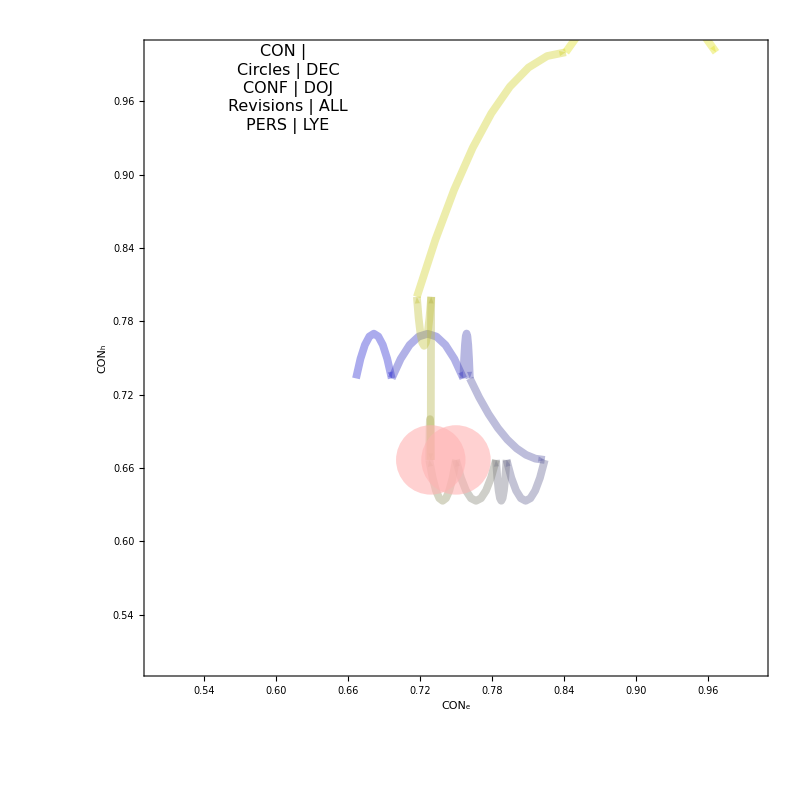
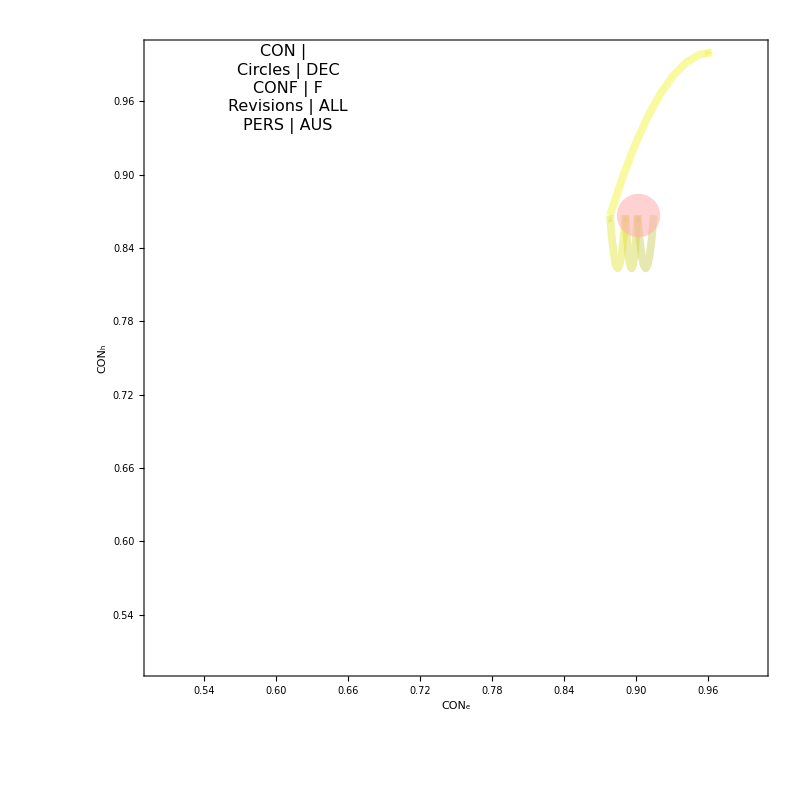

```mathematica
{plotsDOJ[[3]],plotsF[[-1]]}
```

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType]
Export[ToString[plotType]<>"_DOJ.jpeg",gridDOJ]
Export[ToString[plotType]<>"_Z.jpeg",gridZ]
Export[ToString[plotType]<>"_F.jpeg",gridF]
```

/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_INC/RAT_0_99/ALL

DEC_DOJ.jpeg

DEC_Z.jpeg

DEC_F.jpeg